### Categorization

Tutorial

MaTeX

MaTeX`

MaTeX/tutorial/BasicUsage

### Keywords

tex, latex, typesetting, computer modern, latin modern

Details

# Basic Usage

MaTeX can compile inline math-mode LATEX code into Mathematica graphics. It is meant for creating beautiful labels with high quality typesetting for publication figures.

This loads the package:

```mathematica
<<MaTeX`
```

MaTeX["texcode"] | compiles inline math-mode LATEX code
MaTeX[expr] | converts expr to LATEX using TeXForm and compiles the result
MaTeX[{expr_1,expr_2,…}] | compile each expression in a list

Basic MaTeX syntax.

Compile basic LATEX code to Mathematica graphics:

```mathematica
MaTeX["a x^2 + b x + c = 0"]
```

-Graphics-

```mathematica
Head[%]
```

Graphics

Typeset a Mathematica expression:

```mathematica
MaTeX[Expand[(x+y)^5]]
```

-Graphics-

Use HoldForm to prevent evaluating the expression that needs to be typeset:

```mathematica
MaTeX@HoldForm@Sum[1/k^2,{k,1,Infinity}]
```

-Graphics-

Compile multiple expressions in one go:

```mathematica
MaTeX[
Table[
With[{x=Pi/k},HoldForm[Sin[x]]==Sin[x]],
{k,1,6}
]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Typeset a matrix using MatrixForm:

```mathematica
MaTeX@MatrixForm@RotationMatrix[ϑ,{0,0,1}]
```

-Graphics-

Typeset a Mathematica expression in StandardForm instead of converting it to traditional mathematical notation:

```mathematica
MaTeX@StandardForm@TrigExpand[Sin[5x]]
```

-Graphics-

Typeset a system of equations and show it at double size:

```mathematica
MaTeX[
"
\\begin{aligned}
\\nabla\\cdot\\mathbf{E} &= \\frac{\\rho}{\\varepsilon_0} \\\\
\\nabla\\cdot\\mathbf{B} &= 0 \\\\
\\nabla\\times\\mathbf{E} &= 
-\\frac{\\partial \\mathbf{B}}{\\partial t} \\\\
\\nabla\\times\\mathbf{B} &= 
\\mu_0 \\left( \\mathbf{J} + \\varepsilon_0 \\frac{\\partial \\mathbf{E}}{\\partial t} \\right)
\\end{aligned}
",
Magnification->2
]
```

-Graphics-

MaTeX is primarily meant for creating labels for use in publication graphics.

Annotating a plot is possible using Text or Inset:

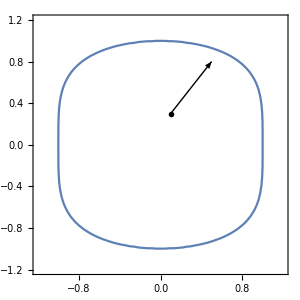

```mathematica
ContourPlot[x^2+y^4==1,{x,-1.2,1.2},{y,-1.2,1.2},
Epilog->{
Arrow[{{0.1,0.3},{0.5,0.80}}],Text[MaTeX["x^2+y^4=1",Magnification->2],{0.1,0.3},Scaled[{0.5,1}]]
},
ImageSize->300
]
```

MaTeX computes the baseline of the output. MaTeX output can be interspersed with standard text without breaking alignment.

```mathematica
Magnify[Style[
StringForm["Squaring `` gives ``.",MaTeX["x"],MaTeX["x^2"]],
FontFamily->"Times"
],3]
```

Squaring … gives ….

## Recommended workflow

When using MaTeX to create multiple labels for publication figures, it is convenient to start by setting promiment options for the session using SetOptions. The settings will persist until the Mathematica kernel is restarted.

option name | default value |  
FontSize | 12 | font size to pass to LATEX
Magnification | 1 | magnification factor to apply to the output
"DisplayStyle" | True | whether to output in display style or inline style
"Preamble" | {} | a list of strings that will be added as lines to the LATEX preamble

Prominent MaTeX options that control formatting.

Unlike Needs, Get re-loads the package even if it has already been loaded and thus resets the options to their defaults:

```mathematica
Get["MaTeX`"]
```

Assuming the target publication recommends using 10-12 point Times font in figures, let us set FontSize→12 and load the txfonts LATEX package in the preamble:

```mathematica
SetOptions[MaTeX,FontSize->12,"Preamble"->{"\\usepackage{txfonts}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{txfonts}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

Let us also define a matching general style that can be used in Style, BaseStyle, etc.

```mathematica
style=Directive[FontFamily->"Times",FontSize->10];
```

It is useful to prepare publication figures to a specific print size. This will allow matching font sizes between the figure and document. Let us define the centimetre unit:

```mathematica
cm=72/2.54; (* 72 points per inch and 1 inch = 2.54 cm *)
```

This is a figure prepared to 6 cm size using the standard styles defined above. This size appears as very small in a Mathematica notebook, so it is best to display it magnified using Magnify:

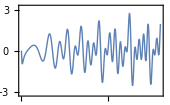

```mathematica
fig=Plot[
Im[Zeta[1/2+ I x]],{x,0,80},
PlotStyle->AbsoluteThickness[1],
ImageSize->6cm (* 6 cm width *),
BaseStyle->style,
Frame->True,FrameStyle->BlackFrame,
PlotRange->3.2{-1,1},
FrameLabel->{MaTeX["x",ContentPadding->False],None},
PlotLabel->MaTeX["\\text{Riemann $\\zeta$ on the critical line}"],
Epilog->{
Text[
MaTeX["\\operatorname{Im}\\zeta(\\frac{1}{2}+ix)","DisplayStyle"->False],
Scaled[{0.23,0.12}]
]
}
];
Magnify[fig,2]
```

The figure can now be exported as a PDF, which will print at exactly the specified size:

```mathematica
Export["figure.pdf",fig]
```

## Matching fonts and styles

By default, LATEX uses the Computer Modern font. It is useful to have a version of this font installed into the operating system, so it can also be used directly in Mathematica for tick labels or in Text primitives.

The following examples use the Latin Modern family of fonts. Note that the name that can be used to recall these fonts may vary by operating system, and the following examples may need to be adjusted accordingly. On OS X, try "Latin Modern Roman". On Windows, try "LM Roman 12".

This loads the package:

```mathematica
<<MaTeX`
```

Since LATEX uses the Computer Modern font by default, it is most convenient to install this font and use it directly for labels, ticks, etc. through BaseStyle.

```mathematica
ContourPlot[{x^2+y^2==1,x^4+y^4==1},{x,-1.2,1.2},{y,-1.2,1.2},
PlotLegends->MaTeX[{x^2+y^2==1,x^4+y^4==1},ContentPadding->False],
FrameLabel->MaTeX[{x,y},ContentPadding->False],
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameStyle->BlackFrame
]
```

-Graphics-

Mathematica draws frames and labels in grey (to be specific, using GrayLevel[0.4]). MaTeX outputs in black by default. To match them, the above example uses FrameStyle->BlackFrame for black frames with a reasonable line weight.

Alternatively, we can change the LATEX font. This is usually done by loading packages. There is a list of such packages at http://www.tug.dk/FontCatalogue/

Use sans-serif fonts:

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{cmbright}"}];
ContourPlot[{x^2+y^2==1,x^4+y^4==1},{x,-1.2,1.2},{y,-1.2,1.2},
PlotLegends->MaTeX[{x^2+y^2==1,x^4+y^4==1},ContentPadding->False],
FrameLabel->MaTeX[{x,y},ContentPadding->False],
FrameStyle->BlackFrame
]
```

-Graphics-

Use the Times font:

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{txfonts}"}];
ContourPlot[{x^2+y^2==1,x^4+y^4==1},{x,-1.2,1.2},{y,-1.2,1.2},
PlotLegends->MaTeX[{x^2+y^2==1,x^4+y^4==1},ContentPadding->False],
FrameLabel->MaTeX[{x,y},ContentPadding->False],
BaseStyle->{FontFamily->"Times"},
FrameStyle->BlackFrame
]
```

-Graphics-

Restore the default preamble:

```mathematica
SetOptions[MaTeX,"Preamble"->{}];
```

When using XeLaTeX, we can use any installed font directly.

Warning: Settings made through ConfigureMaTeX are stored persistently and will not be cleared after restarting Mathematica.

Configure MaTeX to use XeLaTeX:

```mathematica
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/xelatex"]
```

{Ghostscript→/usr/local/bin/gs,CacheSize→100,pdfLaTeX→/Library/TeX/texbin/xelatex}

Change the text mode font:

```mathematica
MaTeX["\\text{Abracadabra}",
"Preamble"->{"\\usepackage{fontspec}","\\setmainfont{Zapfino}"},
FontSize->24
]
```

-Graphics-

Change the math font. This only works with fonts containing an OpenType math table, such as Cambria Math or the STIX fonts:

```mathematica
MaTeX[Expand[(x+1)^3],
"Preamble"->{"\\usepackage{unicode-math}","\\setmathfont{Cambria Math}"},
FontSize->24
]
```

-Graphics-

Colors can be changed either directly in Mathematica, or within LATEX using the color package.

Change colours by post-processing the MaTeX output:

```mathematica
changeStyle[col_][Graphics[items_,opt___]]:=Graphics[{col,items},opt]
```

```mathematica
changeStyle[Orange]/@MaTeX[x^Range[3],Magnification->3]
```

{-Graphics-,-Graphics-,-Graphics-}

Change colours directly in LATEX:

```mathematica
MaTeX["\\frac{\\color{red} x}{1+ {\\color{red} x}}","Preamble"->{"\\usepackage{color}"},Magnification->2]
```

-Graphics-

## Improving performance

MaTeX needs to call LATEX for each expression it typesets. Each call to LATEX is time consuming and typically takes at least about half a second. To mitigate this problem, MaTeX caches results.

This loads the package:

```mathematica
<<MaTeX`
```

### Caching results

The first time an expression is typeset, it usually takes about half a second:

```mathematica
MaTeX[Sin[x]^2+Cos[x]^2==1]//AbsoluteTiming
```

{0.60741,-Graphics-}

Subsequent calls to MaTeX use the cached result and are almost instantaneous:

```mathematica
MaTeX[Sin[x]^2+Cos[x]^2==1]//AbsoluteTiming
```

{0.003,-Graphics-}

Clearing the cache forces LATEX to be run again:

```mathematica
ClearMaTeXCache[]
MaTeX[Sin[x]^2+Cos[x]^2==1]//AbsoluteTiming
```

{0.60407,-Graphics-}

The number of results that are kept cached is limited by default. The cache size can be retrieved or set using ConfigureMaTeX.

Warning: Settings made through ConfigureMaTeX are stored persistently and will not be cleared after restarting Mathematica.

Get the current cache size:

```mathematica
Lookup[ConfigureMaTeX[],"CacheSize"]
```

100

Set the cache size to 0 to disable caching:

```mathematica
ConfigureMaTeX["CacheSize"->0]
```

{Ghostscript→/usr/local/bin/gs,pdfLaTeX→/Library/TeX/texbin/xelatex,CacheSize→0}

Set it to Infinity to cache an unlimited number of results:

```mathematica
ConfigureMaTeX["CacheSize"->Infinity]
```

{Ghostscript→/usr/local/bin/gs,pdfLaTeX→/Library/TeX/texbin/xelatex,CacheSize→∞}

Set it back to the default of 100:

```mathematica
ConfigureMaTeX["CacheSize"->100]
```

{Ghostscript→/usr/local/bin/gs,pdfLaTeX→/Library/TeX/texbin/xelatex,CacheSize→100}

### Typesetting multiple expressions with a single LATEX run

MaTeX threads over lists, and typesets all expressions in the list using only a single call to LATEX. Try to structure your code so it has as few different MaTeX calls as possible.

Typeset 10 expressions separately:

```mathematica
ClearMaTeXCache[]
MaTeX/@(x^Range[10])//AbsoluteTiming
```

{3.52654,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Typeset all 10 using a single function call:

```mathematica
ClearMaTeXCache[]
MaTeX[(x^Range[10])]//AbsoluteTiming
```

{0.42336,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

This technique is particularly useful when typesetting tick labels:

```mathematica
Plot[Sin[x],{x,0,2 Pi},
Frame->True,FrameStyle->BlackFrame,
FrameTicks->{
{Automatic,None},{With[{ticks=Pi/4 Range[0,8]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False,FontSize->14]}]],None}},FrameLabel->MaTeX[{"x","\\sin x"},FontSize->18],
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
ImageSize->Medium]
```

-Graphics-

### Performance depends on the LATEX flavour being used

Performance depends on LATEX executable which is being used. pdflatex is typically the fastest, but it cannot use system fonts directly. xelatex is slower but gives direct and easy access to all fonts installed on the system.

Warning: Settings made through ConfigureMaTeX are stored persistently and will not be cleared after restarting Mathematica.

pdflatex is fast:

```mathematica
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/pdflatex"]
```

{Ghostscript→/usr/local/bin/gs,CacheSize→100,pdfLaTeX→/Library/TeX/texbin/pdflatex}

```mathematica
ClearMaTeXCache[]
MaTeX["x"]//AbsoluteTiming
```

{0.35968,-Graphics-}

xelatex is slower:

```mathematica
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/xelatex"]
```

{Ghostscript→/usr/local/bin/gs,CacheSize→100,pdfLaTeX→/Library/TeX/texbin/xelatex}

```mathematica
ClearMaTeXCache[]
MaTeX["x"]//AbsoluteTiming
```

{0.60406,-Graphics-}

lualatex is generally fast as well:

```mathematica
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/lualatex"]
```

{Ghostscript→/usr/local/bin/gs,CacheSize→100,pdfLaTeX→/Library/TeX/texbin/lualatex}

```mathematica
ClearMaTeXCache[]
MaTeX["x","Preamble"->{"\\usepackage{luatex85}"}]//AbsoluteTiming
```

{0.39779,-Graphics-}

## Implementation notes

MaTeX[expr] generally performs the following steps:

If expr is not a string or other common string-like form, it is converted to LATEX code using TeXForm.

The code, as well as some values controlled by options, is spliced into the following template:

```mathematica
FilePrint@FileNameJoin[{DirectoryName@DirectoryName@FindFile["MaTeX`"],"template.tex"}]
```

\documentclass[12pt, border=1pt, multi]{standalone}
\newenvironment{matex}{\ignorespaces}{\ignorespacesafterend}
\standaloneenv{matex}
\newbox\MaTeXbox
\newcommand{\MaTeX}[1]{
	\begin{matex}
		\setbox\MaTeXbox\hbox{%
			`strut`%
			\(%
				`display`%
				#1%
			\)}%
		\typeout{MATEXDEPTH:\the\dp\MaTeXbox}%
		\typeout{MATEXHEIGHT:\the\ht\MaTeXbox}%
		\typeout{MATEXWIDTH:\the\wd\MaTeXbox}%
		\unhbox\MaTeXbox%
	\end{matex}
}
\usepackage[utf8]{inputenc}
`preamble`
\begin{document}
\fontsize{`fontsize`pt}{`skipsize`pt}\selectfont
`tex`
\end{document}

The resulting .tex file is saved into a temporary directory and compiled using pdflatex.

The PDF output from LATEX is post-processed by Ghostscript using the following options: -dNoOutputFonts -sDEVICE=pdfwrite. This causes the fonts to be outlined and prevents problems when importing the PDF into Mathematica.

The final PDF file is imported back into Mathematica as Graphics using Import[…, "PDF"]. Then ImageSize and BaselinePosition are computed and set using information from the LATEX log file.

More About

Related Tutorials

Related Wolfram Education Group Courses